```mathematica
Quit
```

## Dlogbasis

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"]
```

/Users/corradini/fire/FIRE6

```mathematica
<<DlogBasis`
```

DlogBasis: Package for automated calculation of leading singularities and dlog integrands.
Pascal Wasser, Johannes Gutenberg University Mainz (2020).

```mathematica
Internal= {k1, k2,k3};
External= {p1,p2,p3};
Propagators={-k1^2,-(k1+p1)^2,-(k1+p1+p2)^2,-k2^2,-(k2-k1)^2,-(k3+k2-k1)^2,-(k2+k3+p1+p2)^2,-(k2+k3+p1+p2+p3)^2,-k3^2,-(k2+p1+p2+p3)^2,-(k2+p1)^2,-(k3+p1)^2,-(k1+p1+p2+p3)^2,-(k3+k1)^2,-(k2+p1+p2)^2};
Replacements= {p1^2->0,p2^2->0,p3^2->0,p1 p2->s/2,p1 p3->(-s-t)/2,p2 p3->t/2};
InitializeDlogbasis[];
```

```mathematica
SetParametrization[SpinorHelicityParametrization[Internal,{a,b,c},External]]
```

```mathematica
ansatz=IntegrandAnsatz[G[1,{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0}]];
```

```mathematica
ansatz//Length
```

377

```mathematica
integrand=Parametrize[ansatz,n];
```

```mathematica
leadingsingularities=LeadingSingularities[integrand,IntegrandVariables[],n];
```

```mathematica
dlogs=GenerateDlogbasis[ansatz,leadingsingularities,n];
```

```mathematica
Export["FF/3LTC/dlog.m",(Cases[dlogs,_G,{0,Infinity}]/.{G[1,{a__}]:>{1,{a}}})//DeleteDuplicates]
Export["FF/3LTC/dlogBasis.m",dlogs]
```

FF/3LTC/dlog.m

FF/3LTC/dlogBasis.m

```mathematica
Quit[]
```

## Reduction using FIRE

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
Get["FIRE6.m"];
```

FIRE, version 6.5.2

```mathematica
Internal= {k1, k2,k3};
External= {p1,p2,p3};
Propagators={-k1^2,-(k1+p1)^2,-(k1+p1+p2)^2,-k2^2,-(k2-k1)^2,-(k3+k2-k1)^2,-(k2+k3+p1+p2)^2,-(k2+k3+p1+p2+p3)^2,-k3^2,-(k2+p1+p2+p3)^2,-(k2+p1)^2,-(k3+p1)^2,-(k1+p1+p2+p3)^2,-(k3+k1)^2,-(k2+p1+p2)^2};
Replacements= {p1^2->0,p2^2->0,p3^2->0,p1 p2->s/2,p1 p3->(-s-t)/2,p2 p3->t/2};
```

```mathematica
PrepareIBP[];
Prepare[AutoDetectRestrictions->True,LI->True];
SaveStart["FF/3LTC/3LTC"];
Quit[];
```

Prepared

Dimension set to 15

No symmetries

Saving initial data

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
SetDirectory["extra/LiteRed/Setup/"];
Get["LiteRed.m"];
SetDirectory["../../.."];
Get["FIRE6.m"];
Internal= {k1, k2,k3};
External= {p1,p2,p3};
Propagators={-k1^2,-(k1+p1)^2,-(k1+p1+p2)^2,-k2^2,-(k2-k1)^2,-(k3+k2-k1)^2,-(k2+k3+p1+p2)^2,-(k2+k3+p1+p2+p3)^2,-k3^2,-(k2+p1+p2+p3)^2,-(k2+p1)^2,-(k3+p1)^2,-(k1+p1+p2+p3)^2,-(k3+k1)^2,-(k2+p1+p2)^2};
Replacements= {p1^2->0,p2^2->0,p3^2->0,p1 p2->s/2,p1 p3->(-s-t)/2,p2 p3->t/2};
CreateNewBasis[b1,Directory->"./b3LTC.dir"];
GenerateIBP[b1];
AnalyzeSectors[b1,{__,0,0,0,0,0}];
FindSymmetries[b1,EMs->True];
DiskSave[b1];
Quit[];
```

**************** LiteRed v1.83 ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: 11.01.2020
LiteRed stands for Loop InTEgrals REDuction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.
Input file timestamp: Sun 7 Sep 2025 15:59:28
See ?LiteRed`* for a list of functions.

FIRE, version 6.5.2

Declare: {{k1,k2,k3,p1,p2,p3},Vector,{s,t},Number}

Lee propagators: {-(k1·k1),-((k1+p1)·(k1+p1)),-((k1+p1+p2)·(k1+p1+p2)),-(k2·k2),-((-k1+k2)·(-k1+k2)),-((-k1+k2+k3)·(-k1+k2+k3)),-((k2+k3+p1+p2)·(k2+k3+p1+p2)),-((k2+k3+p1+p2+p3)·(k2+k3+p1+p2+p3)),-(k3·k3),-((k2+p1+p2+p3)·(k2+p1+p2+p3)),-((k2+p1)·(k2+p1)),-((k3+p1)·(k3+p1)),-((k1+p1+p2+p3)·(k1+p1+p2+p3)),-((k1+k3)·(k1+k3)),-((k2+p1+p2)·(k2+p1+p2))}

Valid basis.
    Ds[b1] — denominators,
    SPs[b1] — scalar products involving loop momenta,
    LMs[b1] — loop momenta,
    EMs[b1] — external momenta,
    Toj[b1] — rules to transform scalar products to denominators.
The definitions of the basis will be saved in ./b3LTC.dir

DiskSave::overwrite: The file ./b3LTC.dir/b1 has been overwritten.

Integration-By-Part&Lorentz-Invariance identities are generated.
    IBP[b1] — integration-by-part identities,
    LI[b1] — Lorentz invariance identities.

Found 720 zero sectors out of 1024.
    ZeroSectors[b1] — zero sectors,
    NonZeroSectors[b1] — nonzero sectors,
    SimpleSectors[b1] — simple sectors (no nonzero subsectors),
    BasisSectors[b1] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[b1] — a rule to nullify all zero j[b1…],
    CutDs[b1] — a flag list of cut denominatorsj (1=cut).

Found 172 mapped sectors and 132 unique sectors.
    UniqueSectors[b1] — unique sectors.
    MappedSectors[b1] — mapped sectors.
    SR[b1][…] — symmetry relations for j[b1,…] from UniqueSectors[b1].
    jSymmetries[b1,…] — symmetry rules for the sector js[b1,…] in UniqueSectors[b1].
    jRules[b1,…] — reduction rules for j[b1,…] from MappedSectors[b1].

DiskSave::overwrite: The file BasisSectors[b1] has been overwritten.

DiskSave::overwrite: The file IBP[b1] has been overwritten.

DiskSave::overwrite: The file jRules[b1, 0, 0, 0, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0] has been overwritten.

General::stop: Further output of DiskSave::overwrite will be suppressed during this calculation.

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
Get["FIRE6.m"];
LoadStart["FF/3LTC/3LTC"];
TransformRules["./b3LTC.dir","FF/3LTC/3LTC.lbases",1];
SaveSBases["FF/3LTC/3LTC"];
Quit[];
```

```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
Get["FIRE6.m"];
LoadStart["FF/3LTC/3LTC",1];
Burn[];
LoadTables["FF/3LTC/3LTC.tables"];
```

FIRE, version 6.5.2

Initial data loaded

```mathematica
InvCh=(Import["FF/3LTC/dlogBasis.m"]/.{G->F});
```

```mathematica
InvCh//Length
```

168

```mathematica
Export["FF/3LTC/mastersLad.m",F[1,{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0}]];
Export["FF/3LTC/mastersLadCan.m",MasterIntegrals[]];
Export["FF/3LTC/invCh.m",InvCh];
```

## Change of basis from the canonical basis to the ‘Laporta’ one

```mathematica
Quit
```

```mathematica
<<FiniteFlow`
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
```

```mathematica
Can=Import["FF/3LTC/dlogBasis.m"];
InvCh=Import["FF/3LTC/invCh.m"];
masters=Import["FF/3LTC/mastersLadCan.m"]/.{{1,{a__}}->G[1,{a}]};
```

```mathematica
cs=Table[c[i],{i,1,Length[InvCh]}];
```

```mathematica
eqs=Table[
Coefficient[cs[[i]]InvCh[[i]],
masters],{i,Length[InvCh]}];
```

```mathematica
mysys = (Thread[Total[eqs]==0]//Collect[#,_c,Together]&)/.{d->4-2eps};
```

```mathematica
mysol = FFDenseSolve[mysys,cs];
```

```mathematica
mysol//Length
```

41

```mathematica
todel=(Cases[cs/.mysol,_c,Infinity]//DeleteDuplicates)/.c->List;
```

```mathematica
todel//Length
```

127

```mathematica
newCh=Delete[InvCh,todel];
newCan=Delete[Can,todel];
```

```mathematica
newCan//Length
```

41

```mathematica
Ms=Array[M,Length[masters]];
Gs=Array[G,Length[newCh]];
```

```mathematica
ChMat=Table[
Coefficient[newCh[[i]],
masters[[k]]],{i,Length[newCh]},{k,Length[masters]}];
```

```mathematica
BasisChange=FFInverse[ChMat/.{d->4-2eps}//Together,Parameters->{s,t,eps}];
```

```mathematica
Export["FF/3LTC/can.m",newCan];
Export["FF/3LTC/BasisCh.m",newCh];
Export["FF/3LTC/MIstoCan.m",BasisChange];
```

```mathematica
"FF/3LTC/can.m"
```

```mathematica
"FF/3LTC/MIstoCan.m"
```

```mathematica
"FF/3LTC/BasisCh.m"
```

```mathematica
Quit
```

```mathematica
"FF/3LTC/BoxinCan.m"
```

## Draw MIs

```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
```

```mathematica
<<LiteRed2`
```

**************** LiteRed v2.025β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Thu 20 Nov 2025 13:50:10
Read from:/Users/corradini/LiteRed2/Source/LiteRed2025.m (CRC32:749265139,{2340977437, 3317197336, 1063727846})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

```mathematica
Declare[{k1,k2,k3,p1,p2,p3},Vector,{s,t},Number];
```

```mathematica
sp[p1,p1]=0;sp[p2,p2]=0;sp[p3,p3]=0;sp[p1,p2]=s/2;sp[p2,p3]=t/2;sp[p1,p3]=(-s-t)/2;
```

```mathematica
NewDsBasis[box3,{-(k1·k1),-((k1+p1)·(k1+p1)),-((k1+p1+p2)·(k1+p1+p2)),-(k2·k2),-((-k1+k2)·(-k1+k2)),-((-k1+k2+k3)·(-k1+k2+k3)),-((k2+k3+p1+p2)·(k2+k3+p1+p2)),-((k2+k3+p1+p2+p3)·(k2+k3+p1+p2+p3)),-(k3·k3),-((k2+p1+p2+p3)·(k2+p1+p2+p3)),-((k2+p1)·(k2+p1)),-((k3+p1)·(k3+p1)),-((k1+p1+p2+p3)·(k1+p1+p2+p3)),-((k1+k3)·(k1+k3)),-((k2+p1+p2)·(k2+p1+p2))},{k1,k2,k3},Directory->"box3dir"];
```

box3 is valid basis. The definitions of the basis will be saved in "box3dir" directory.
    Ds[box3] — denominators,
    SPs[box3] — scalar products involving loop momenta,
    LMs[box3] — loop momenta,
    EMs[box3] — external momenta,
    Parameters[box3] — parameters (invariants, masses, dimension),
    Toj[box3] — rules to transform scalar products to denominators,
    CutDs[box3] — flag vector of cut denominators.

```mathematica
topo={{8->1,0},{1->2,0},{2->3,0},{6->8,0},{8->7,0},{7->3,0},{3->5,0},{5->4,0},{4->7,0},{4->6,0},{-1->1,p1,0},{-2->2,p2,0},{-5->5,p3,0},{-6->6,p4,0}};
```

```mathematica
SetOptions[FeynGraphPlot,EdgeLabels->True,Frame->False]
```

{GraphLayout→SpringElectricalEmbedding,VertexCoordinates→Automatic,EdgeLabels→True,EdgeStyle→{_→{GrayLevel[0]}},VertexStyle→{_→{GrayLevel[0],Disk[{0,0}]}},VertexSize→{_→0.003},VertexLabels→None,VertexLabelStyle→{RGBColor[1, 0, 0]},Background→None,Frame→False,FrameLabel→None,FrameStyle→{},LabelStyle→{},ImageMargins→0,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→RGBColor[1, 0, 0],MultiedgeStyle→Automatic,PackingMethod→Automatic,PlotLabel→None,Epilog→{}}

```mathematica
AttachGraph[js[box3,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0],topo]
```

```mathematica
masters=Import["FF/3LTC/mastersLadCan.m"]/.{_,{a__}}:>j[box3,a]
```

{j[box3,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0],j[box3,0,0,1,1,1,0,0,1,1,0,0,0,0,0,0],j[box3,0,0,1,1,1,0,1,0,1,0,0,0,0,0,0],j[box3,0,0,1,1,1,1,0,1,1,0,0,0,0,0,0],j[box3,0,1,0,0,0,1,0,0,1,1,0,0,0,0,0],j[box3,0,1,0,0,1,0,1,0,1,1,0,0,0,0,0],j[box3,0,1,0,0,1,1,0,1,0,1,0,0,0,0,0],j[box3,0,1,0,0,1,1,1,0,1,1,0,0,0,0,0],j[box3,0,1,0,1,0,1,1,0,1,1,0,0,0,0,0],j[box3,0,1,0,1,0,1,1,1,1,0,0,0,0,0,0],j[box3,0,1,0,1,1,1,1,0,0,1,0,0,0,0,0],j[box3,0,1,0,1,1,1,1,0,1,1,0,0,0,0,0],j[box3,0,1,0,1,1,1,1,0,1,2,0,0,0,0,0],j[box3,0,1,0,1,1,1,1,1,0,1,0,0,0,0,0],j[box3,0,1,0,1,1,1,1,1,1,1,0,0,0,0,0],j[box3,0,1,0,1,1,1,1,1,1,2,0,0,0,0,0],j[box3,0,1,0,1,1,1,2,1,0,1,0,0,0,0,0],j[box3,0,1,1,1,0,1,0,0,1,1,0,0,0,0,0],j[box3,0,1,1,1,1,0,1,0,1,1,0,0,0,0,0],j[box3,0,1,1,1,1,0,1,1,1,0,0,0,0,0,0],j[box3,0,1,1,1,1,0,1,1,2,0,0,0,0,0,0],j[box3,0,1,1,1,1,1,0,1,0,1,0,0,0,0,0],j[box3,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0],j[box3,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0],j[box3,0,1,1,1,1,1,1,2,1,0,0,0,0,0,0],j[box3,1,0,1,0,0,1,0,0,1,1,0,0,0,0,0],j[box3,1,0,1,0,1,0,1,0,1,1,0,0,0,0,0],j[box3,1,0,1,0,1,1,0,1,0,1,0,0,0,0,0],j[box3,1,0,1,1,0,0,1,0,1,0,0,0,0,0,0],j[box3,1,0,1,1,0,1,1,0,1,1,0,0,0,0,0],j[box3,1,0,1,1,1,1,1,1,1,1,0,0,0,0,0],j[box3,1,1,1,0,0,1,0,0,1,1,0,0,0,0,0],j[box3,1,1,1,0,1,0,1,0,1,1,0,0,0,0,0],j[box3,1,1,1,0,1,1,0,1,0,1,0,0,0,0,0],j[box3,1,1,1,1,0,1,1,0,1,1,0,0,0,0,0],j[box3,1,1,1,1,0,1,1,0,1,2,0,0,0,0,0],j[box3,1,1,1,1,0,1,1,1,1,0,0,0,0,0,0],j[box3,1,1,1,1,0,1,1,2,1,0,0,0,0,0,0],j[box3,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0],j[box3,1,1,1,1,1,1,1,1,1,2,0,0,0,0,0],j[box3,1,1,1,1,1,1,1,1,2,1,0,0,0,0,0]}

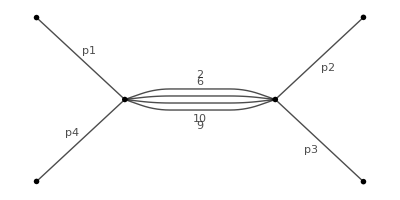
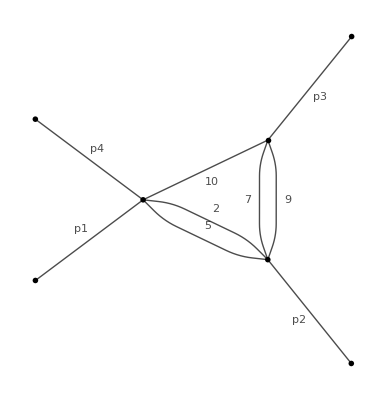
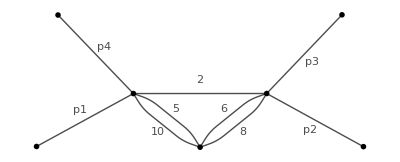
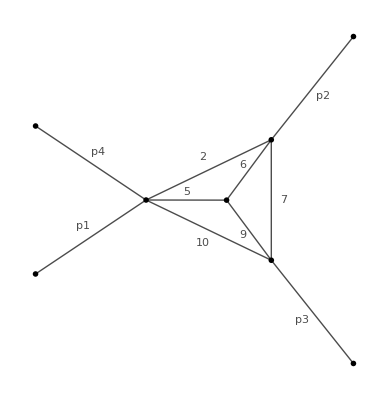

```mathematica
jGraphPlot/@masters[[{5,6,7,8}]]
```

```mathematica
canonicalmasters=Import["FF/3LTC/can.m"]/.{_,{a__}}:>j[box3,a];
```

{GraphLayout→SpringElectricalEmbedding,VertexCoordinates→Automatic,EdgeLabels→False,EdgeStyle→{_→{GrayLevel[0]}},VertexStyle→{_→{GrayLevel[0],Disk[{0,0}]}},VertexSize→{_→0.003},VertexLabels→None,VertexLabelStyle→{RGBColor[1, 0, 0]},Background→None,Frame→False,FrameLabel→None,FrameStyle→{},LabelStyle→{},ImageMargins→0,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→RGBColor[1, 0, 0],MultiedgeStyle→Automatic,PackingMethod→Automatic,PlotLabel→None,Epilog→{}}

jGraph::nums: The numerator is not drawn!.

General::stop: Further output of jGraph::nums will be suppressed during this calculation.

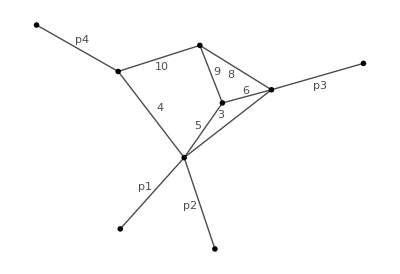
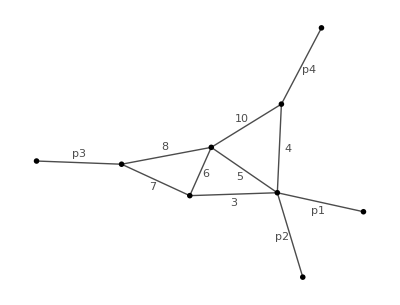
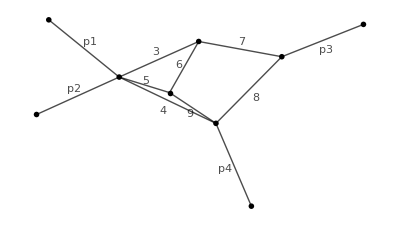
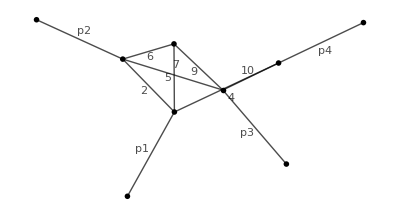
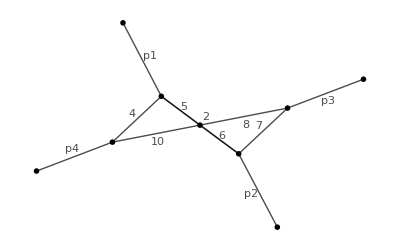
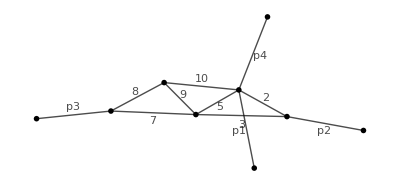
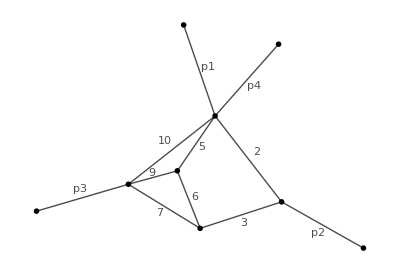
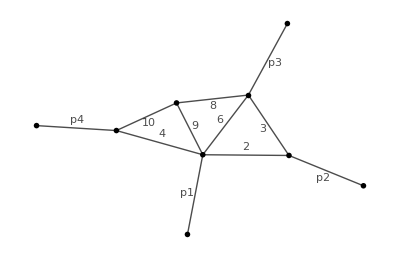
{s -Graphics-,s -Graphics-,s -Graphics-,t -Graphics-,(s+t) -Graphics-,s -Graphics-,t -Graphics-,t -Graphics-,(s+t) -Graphics-,(s+t) -Graphics-,t -Graphics-,s -Graphics-,s -Graphics-,s t -Graphics-,s t -Graphics-,s t -Graphics-,s t -Graphics-,s t -Graphics-,s^2 -Graphics-,s^2 -Graphics-,s t -Graphics-,s t -Graphics-,s^2 -Graphics-,s (s+t) -Graphics-,t -Graphics-+s t -Graphics-,s -Graphics-+s t -Graphics-,s -Graphics--t -Graphics-+t -Graphics--t -Graphics-,t -Graphics-,-2 s -Graphics--s -Graphics-+s -Graphics-+s -Graphics-,t -Graphics-+s -Graphics-,s -Graphics-,t -Graphics-+s -Graphics-+s t -Graphics-,s^2 t -Graphics-,s t -Graphics-,s^2 -Graphics-,s t -Graphics-,s^2 -Graphics-,-s^2 -Graphics--2 s^2 -Graphics-+2 s^2 -Graphics-,s^2 t -Graphics-,s^2 -Graphics-,-s t -Graphics-+s t -Graphics-+s t -Graphics-}

```mathematica
canonicalmasters/.Thread[Cases[canonicalmasters,_G,Infinity]->jGraphPlot/@(Cases[canonicalmasters,_G,Infinity]/.G[_,{a__}]:>j[box3,a])]
```

## Differential equations matrix

```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
```

```mathematica
<<LiteRed2`
```

**************** LiteRed v2.025β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Thu 20 Nov 2025 13:50:10
Read from:/Users/corradini/LiteRed2/Source/LiteRed2025.m (CRC32:749265139,{2340977437, 3317197336, 1063727846})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

```mathematica
Declare[{k1,k2,k3,p1,p2,p3},Vector,{s,t},Number];
sp[p1,p1]=0;sp[p2,p2]=0;sp[p3,p3]=0;sp[p1,p2]=s/2;sp[p2,p3]=t/2;sp[p1,p3]=(-s-t)/2;
```

```mathematica
NewDsBasis[box3,{-(k1·k1),-((k1+p1)·(k1+p1)),-((k1+p1+p2)·(k1+p1+p2)),-(k2·k2),-((-k1+k2)·(-k1+k2)),-((-k1+k2+k3)·(-k1+k2+k3)),-((k2+k3+p1+p2)·(k2+k3+p1+p2)),-((k2+k3+p1+p2+p3)·(k2+k3+p1+p2+p3)),-(k3·k3),-((k2+p1+p2+p3)·(k2+p1+p2+p3)),-((k2+p1)·(k2+p1)),-((k3+p1)·(k3+p1)),-((k1+p1+p2+p3)·(k1+p1+p2+p3)),-((k1+k3)·(k1+k3)),-((k2+p1+p2)·(k2+p1+p2))},{k1,k2,k3},Directory->"box3dir"];
```

box3 is valid basis. The definitions of the basis will be saved in "box3dir" directory.
    Ds[box3] — denominators,
    SPs[box3] — scalar products involving loop momenta,
    LMs[box3] — loop momenta,
    EMs[box3] — external momenta,
    Parameters[box3] — parameters (invariants, masses, dimension),
    Toj[box3] — rules to transform scalar products to denominators,
    CutDs[box3] — flag vector of cut denominators.

```mathematica
GenerateIBP[box3]
AnalyzeSectors[box3,{__,0,0,0,0,0}]
FindSymmetries[box3]
```

Identities are generated.
    IBP[box3] — integration-by-part identities,
    LI[box3] — Lorentz invariance identities.

Updated SectorsPattern[box3] — pattern for all relevant sectors of the basis box3.

Found 720(304) zero(nonzero) sectors out of 1024.
    ZeroSectors[box3] — zero sectors,
    NonZeroSectors[box3] — nonzero sectors,
    SimpleSectors[box3] — simple sectors (no nonzero subsectors),
    BasisSectors[box3] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[box3] — a rule to nullify all zero j[box3…],
    CutDs[box3] — a flag list of cut denominators (1=cut).

Found 172 mapped sectors and 132 unique sectors.
    UniqueSectors[box3] — unique sectors.
    MappedSectors[box3] — mapped sectors.
    SR[box3][…] — symmetry relations for j[box3,…] from UniqueSectors[box3].
    jSymmetries[box3,…] — symmetry rules for the sector js[box3,…] in UniqueSectors[box3].
    jRules[box3,…] — reduction rules for j[box3,…] from MappedSectors[box3].
    SectorsMappings[box3] gives the list of mappings of all sectors from MappedSectors[box3] to UniqueSectors[box3].

172

```mathematica
SectorOf[family_,exponents___]:=js[family,##]&@@(If[#>0,1,0]&/@{exponents});
SectorOf[j[family_,exponents___]]:=SectorOf[family,exponents];
```

```mathematica
ZeroQ[j[family_,a__]]:=MemberQ[ZeroSectors[family],SectorOf[j[family,a]]];
```

```mathematica
RemoveZeroSectors[expr_]:=expr /. Dispatch[(#->0)&/@Select[Cases[{expr},_j,Infinity]//DeleteDuplicates,ZeroQ]];
```

```mathematica
can=Import["FF/3LTC/BasisCh.m"]/.G[_,{a__}]:>j[box3,a];
```

```mathematica
ders=Dinv[#,s]&/@can//RemoveZeroSectors;
dert=Dinv[#,t]&/@can//RemoveZeroSectors;
```

```mathematica
Export["FF/3LTC/ders.m",ders];
Export["FF/3LTC/dert.m",dert];
```

```mathematica
jsder=Cases[Join[ders,dert],_j,Infinity]//DeleteDuplicates;
```

```mathematica
Export["FF/3LTC/wishlist_der.m",jsder/.{j[box3,a__]:>{1,{a}}}];
```

```mathematica
"FF/3LTC/wishlist_der.m"
```

```mathematica
Quit
```

### Run IBP reduction with 3LTCDer.config

## Build DE matrix

```mathematica
Quit
```

```mathematica
mastersLaporta=Import["FF/3LTC/mastersLadCan.m"];
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
Get["FIRE6.m"];
LoadStart["FF/3LTC/3LTC",1];
Burn[];
LoadTables["FF/3LTC/3LTCDer.tables"];
```

FIRE, version 6.5.2

Initial data loaded

```mathematica
masters=MasterIntegrals[];
```

```mathematica
SameQ[mastersLaporta,masters]
```

True

```mathematica
ders=(Import["FF/3LTC/ders.m"]/.j[_,a__]:>F[1,{a}]);
dert=(Import["FF/3LTC/dert.m"]/.j[_,a__]:>F[1,{a}]);
ders//Length
```

41

```mathematica
ds0=Table[Coefficient[ders[[i]],(masters[[k]]/.{{1,{a__}}:>G[1,{a}]})],{i,Length[ders]},{k,Length[masters]}];
dt0=Table[Coefficient[dert[[i]],(masters[[k]]/.{{1,{a__}}:>G[1,{a}]})],{i,Length[ders]},{k,Length[masters]}];
```

```mathematica
MIstoCanMatrix=Import["FF/3LTC/MIstoCan.m"];
```

```mathematica
ds=((ds0.MIstoCanMatrix)/.{d->4-2 eps})//Simplify;
dt=((dt0.MIstoCanMatrix)/.{d->4-2 eps})//Simplify;
```

```mathematica
Export["FF/3LTC/ds.m",ds];
Export["FF/3LTC/dt.m",dt];
```

## A first check: scaling and integrability conditions

```mathematica
s ds+t dt//Simplify//MatrixForm
```

(-3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps)

```mathematica
ds.dt-dt.ds-D[ds,t]+D[dt,s]//Simplify//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Integrating the equations

## Computing integrated matrix in x=t/s

```mathematica
alpha={s,t,s+t}
```

{s,t,s+t}

```mathematica
cs=c/@Range[Length[alpha]];
```

```mathematica
eqss=Table[Table[eqs[ii,jj],{jj,1,Length[ds]}],{ii,1,Length[ds]}];
eqts=Table[Table[eqt[ii,jj],{jj,1,Length[dt]}],{ii,1,Length[dt]}];
```

```mathematica
Do[eqs[ii,jj]=ds[[ii]][[jj]]==D[cs.(Log[#]&/@alpha),s],{ii,1,Length[ds]},{jj,1,Length[ds]}];
Do[eqt[ii,jj]=dt[[ii]][[jj]]==D[cs.(Log[#]&/@alpha),t],{ii,1,Length[dt]},{jj,1,Length[dt]}];
```

```mathematica
num50=Table[{s->RandomReal[WorkingPrecision->50],t->RandomReal[WorkingPrecision->50]},{i,1,50}];
```

```mathematica
Do[Do[Asol[ii,jj]=NSolve[Flatten[Table[{eqs[ii,jj],eqt[ii,jj]}/.num50[[iter]],{iter,1,20}]],cs]//Chop//Rationalize;If[Mod[ii,50]==0&&Mod[jj,50]==0,PrintTemporary["Done :: {",ii,",",jj,"}"]];,{ii,1,Length[ds]}],{jj,1,Length[ds]}]
```

```mathematica
Atilde=Table[Table[(cs.(Log[#]&/@alpha))/.Flatten[Asol[ii,jj]],{jj,1,Length[ds]}],{ii,1,Length[ds]}]/._c->0;
Atildex=Collect[Atilde/.t->x s/.s->-1/.Log[a___]:>PowerExpand[Log[Factor[a]]]/.Log[-1-x]:>Log[1+x]/.Pi->0,Log[___],Together];
```

```mathematica
Export["FF/3LTC/Atilde.m",Atildex]
```

FF/3LTC/Atilde.m

## Integrating the differential equations

```mathematica
Quit[]
```

```mathematica
<<PolyLogTools`;
```

(****** PolyLogTools 1.4 ******)

Authors: Claude Duhr, Falko Dulat

Email: cduhr@uni-bonn.de

PolyLogTools uses the implementation of the PSLQ algorithm by P. Bertok (http://library.wolfram.com/infocenter/MathSource/4263/)

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set loaded for weights: 2, 3, 4, 5, 6.

Rules for minimal set for + - weights loaded for weights: 2, 3, 4, 5, 6.

Table of MZVs loaded up to weight 6

Table of values at I loaded up to weight 6

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

GraphJoin::shdw: Symbol GraphJoin appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphProduct::shdw: Symbol GraphProduct appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphSum::shdw: Symbol GraphSum appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

SetDelayed::write: Tag EdgeChromaticNumber in EdgeChromaticNumber[g_Graph] is Protected.

SetDelayed::write: Tag TreeQ in TreeQ[g_Graph] is Protected.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/corradini/fire/FIRE6/FF/3LTC

```mathematica
Atildex=Import["Atilde.m"];
```

```mathematica
Atildex//Variables
```

{eps,Log[x],Log[1+x]}

```mathematica
alphaco=Log[#]&/@{x,1+x};
```

### Weight 0

```mathematica
bdry0[0]=Table[b[i,0],{i,1,41}];
```

```mathematica
Table[A[i]=Coefficient[ Atildex,alphaco[[i]]],{i,1,2}];
```

```mathematica
Table[matexp[i]=MatrixExp[ Log[a] A[i]],{i,2}];
```

```mathematica
eqs[1][0]=Thread[((Series[(x+1)D[Atildex,x],{x,-1,0}]//Normal).bdry0[0])==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[2][0]=Thread[(Coefficient[matexp[1],a^eps].(bdry0[0]))==0]//DeleteCases[#,True]&;
```

```mathematica
sols[1][0]=Solve[Join[Join[eqs[1][0],eqs[2][0]]],bdry0[0]][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryt[0]=bdry0[0]/.sols[1][0];
```

#### Weight 1

```mathematica
bdry0[1]=eps Table[b[i,1],{i,1,Length[bdry0[0]]}];
```

```mathematica
Mbt[1][0]=Map[GIntegrate[#,x]&,D[Simplify[Atildex.bdryt[0]],x]];
```

```mathematica
M0[1]=Mbt[1][0]+bdry0[1];
```

#### Fix remaining weight 0 constants

```mathematica
eqs[3][0]=Thread[(Im[(Series[(x+1)D[Atildex,x],{x,-1,0}]//Normal).M0[1]/.x->-1]//ComplexExpand)==0]//DeleteCases[#,True]&;
```

```mathematica
sols[2][0]=Solve[eqs[3][0],bdry0[0]][[1]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{b[1,0]→0,b[2,0]→0,b[3,0]→0,b[4,0]→0,b[7,0]→0,b[8,0]→0,b[11,0]→0,b[18,0]→-3 b[28,0],b[19,0]→-2 b[28,0],b[21,0]→0,b[23,0]→-9 b[28,0],b[26,0]→0,b[29,0]→6 b[28,0],b[36,0]→-4 b[28,0],b[39,0]→64 b[28,0]}

```mathematica
bdryf[0]=bdryt[0]/.sols[2][0]/.{b[28,0]->61/(108eps^6)}
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,-61/(9 eps^6),-61/(36 eps^6),0,0,-61/(36 eps^6),-61/(54 eps^6),0,0,0,-61/(12 eps^6),0,0,0,0,61/(108 eps^6),61/(18 eps^6),0,0,0,2135/(108 eps^6),-427/(108 eps^6),-61/(108 eps^6),-61/(27 eps^6),-61/(6 eps^6),-671/(108 eps^6),976/(27 eps^6),-427/(27 eps^6),-610/(27 eps^6)}

```mathematica
Mf[0]=bdryf[0]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,-61/(9 eps^6),-61/(36 eps^6),0,0,-61/(36 eps^6),-61/(54 eps^6),0,0,0,-61/(12 eps^6),0,0,0,0,61/(108 eps^6),61/(18 eps^6),0,0,0,2135/(108 eps^6),-427/(108 eps^6),-61/(108 eps^6),-61/(27 eps^6),-61/(6 eps^6),-671/(108 eps^6),976/(27 eps^6),-427/(27 eps^6),-610/(27 eps^6)}

#### Fix weight 1 constants

```mathematica
Mbf[1][0]=Map[GIntegrate[#,x]&,D[Simplify[Atildex.bdryf[0]],x]];
```

```mathematica
Mt[1]=Mbf[1][0]+bdry0[1]
```

{eps b[1,1],eps b[2,1],eps b[3,1],eps b[4,1],eps b[5,1],eps b[6,1],eps b[7,1],eps b[8,1],eps b[9,1],eps b[10,1],eps b[11,1],eps b[12,1],eps b[13,1],eps b[14,1]+(61 G[0,x])/(6 eps^5),eps b[15,1]+(61 G[0,x])/(12 eps^5),eps b[16,1],eps b[17,1],eps b[18,1],eps b[19,1],eps b[20,1],eps b[21,1],eps b[22,1],eps b[23,1],eps b[24,1],eps b[25,1],eps b[26,1],eps b[27,1],eps b[28,1]-(61 G[0,x])/(36 eps^5),eps b[29,1]-(61 G[0,x])/(12 eps^5),eps b[30,1],eps b[31,1],eps b[32,1],eps b[33,1]-(61 G[0,x])/(3 eps^5),eps b[34,1]+(427 G[0,x])/(36 eps^5),eps b[35,1],eps b[36,1]+(61 G[0,x])/(9 eps^5),eps b[37,1]+(61 G[0,x])/(12 eps^5),eps b[38,1]+(61 G[0,x])/(6 eps^5),eps b[39,1]-(1159 G[0,x])/(18 eps^5),eps b[40,1]+(61 G[0,x])/(3 eps^5),eps b[41,1]+(2257 G[0,x])/(36 eps^5)}

```mathematica
eqs[1][1]=Thread[(Re[(Series[(x+1)D[Atildex,x],{x,-1,0}]//Normal).Mt[1]/.x->-1]//ComplexExpand)==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[2][1]=Thread[(Coefficient[matexp[1],a^eps].Mt[1]//Simplify)==0]//DeleteCases[#,True]&;
```

```mathematica
Join[eqs[1][1],eqs[2][1]];
```

```mathematica
sols[1][1]=Solve[Join[Join[eqs[1][1],eqs[2][1]]],bdry0[1]/eps][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryt[1]=bdry0[1]/.sols[1][1]
```

{eps b[1,1],eps b[2,1],eps b[3,1],eps b[4,1],0,eps (b[2,1]-4 b[4,1]+6 b[7,1]-3 b[8,1]+b[18,1]-3 b[28,1]+b[29,1]),eps b[7,1],eps b[8,1],0,0,eps b[11,1],eps (-b[7,1]-1/4 b[21,1]),1/2 eps b[11,1],-2 eps b[29,1],eps (-3 b[1,1]-3 b[2,1]-2 b[3,1]-6 b[4,1]+2 b[7,1]-6 b[8,1]+b[11,1]-3 b[28,1]),eps (-4 b[1,1]-4 b[4,1]),eps (-4 b[3,1]-4 b[8,1]),eps b[18,1],eps b[19,1],eps (-4 b[1,1]+2 b[2,1]-6 b[3,1]-4 b[4,1]+2 b[7,1]-4 b[8,1]+b[19,1]-2 b[28,1]+2/3 b[29,1]),eps b[21,1],eps (6 b[1,1]-2 b[2,1]+4 b[7,1]-4 b[8,1]+b[21,1]),eps b[23,1],0,eps (15/4 b[1,1]-9/4 b[2,1]-5/2 b[3,1]+3/2 b[7,1]-9/2 b[8,1]+3/4 b[11,1]),eps b[26,1],eps (-2 b[4,1]-b[26,1]),eps b[28,1],eps b[29,1],eps (-15/4 b[1,1]+9/4 b[2,1]+3/2 b[3,1]-3/2 b[7,1]+9/2 b[8,1]-3/4 b[11,1]),eps (-b[28,1]-1/4 b[36,1]),-3/2 eps b[11,1],eps (12 b[1,1]+18 b[2,1]+8 b[3,1]+36 b[4,1]-20 b[7,1]+36 b[8,1]+1/2 b[11,1]-b[19,1]-9/4 b[21,1]-3 b[23,1]+18 b[28,1]-2 b[29,1]),eps (-9/2 b[1,1]-3/2 b[2,1]-7 b[3,1]-56/3 b[4,1]+19 b[7,1]-14 b[8,1]+1/2 b[11,1]+2 b[18,1]-5/3 b[26,1]-13 b[28,1]+2 b[29,1]),eps (35/2 b[1,1]+227/14 b[2,1]+11 b[3,1]+1252/21 b[4,1]-337/7 b[7,1]+314/7 b[8,1]+1/2 b[11,1]-20/7 b[18,1]+6/7 b[19,1]-15/7 b[21,1]-18/7 b[23,1]+55/21 b[26,1]+249/7 b[28,1]-152/21 b[29,1]+1/14 b[36,1]-5/14 b[39,1]),eps b[36,1],eps (-9 b[1,1]-15 b[2,1]-6 b[3,1]-30 b[4,1]+18 b[7,1]-30 b[8,1]-3/2 b[11,1]+9/4 b[21,1]+3 b[23,1]-15 b[28,1]+4 b[29,1]),eps (-6 b[1,1]-10 b[2,1]-4 b[3,1]-20 b[4,1]+12 b[7,1]-20 b[8,1]-b[11,1]+1/2 b[21,1]+b[23,1]-10 b[28,1]+4/3 b[29,1]),eps b[39,1],eps (-101/4 b[1,1]-1091/28 b[2,1]-41/2 b[3,1]-1826/21 b[4,1]+835/14 b[7,1]-1181/14 b[8,1]-7/4 b[11,1]+6/7 b[18,1]-6/7 b[19,1]+123/28 b[21,1]+39/7 b[23,1]-20/21 b[26,1]-319/7 b[28,1]+271/21 b[29,1]-1/14 b[36,1]-1/7 b[39,1]),eps (117 b[1,1]+1818/7 b[2,1]+90 b[3,1]+3292/7 b[4,1]-2178/7 b[7,1]+3387/7 b[8,1]+9 b[11,1]+15/7 b[18,1]+90/7 b[19,1]-387/14 b[21,1]-228/7 b[23,1]-5/7 b[26,1]+1635/7 b[28,1]-564/7 b[29,1]-13/14 b[36,1]-6/7 b[39,1])}

### Weight 2

```mathematica
bdry0[2]=eps^2 Table[b[i,2],{i,1,Length[bdry0[0]]}];
Mbf[2][0]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[1][0])];
Mbt[1][1]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryt[1]];
```

```mathematica
M0[2]=Mbf[2][0]+Mbt[1][1]+bdry0[2];
```

#### Fix remaining weight 1 constants

```mathematica
eqs[3][1]=Thread[(Im[(Series[(x+1)D[Atildex,x],{x,-1,0}]//Normal).M0[2]/.x->-1]//ComplexExpand)==0]//DeleteCases[#,True]&;
```

```mathematica
sols[2][1]=Solve[eqs[3][1],bdry0[1]/eps][[1]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{b[1,1]→0,b[2,1]→0,b[3,1]→0,b[4,1]→0,b[7,1]→0,b[8,1]→0,b[11,1]→0,b[18,1]→-3 b[28,1],b[19,1]→-2 b[28,1],b[21,1]→0,b[23,1]→-9 b[28,1],b[26,1]→0,b[29,1]→6 b[28,1],b[36,1]→-4 b[28,1],b[39,1]→64 b[28,1]}

```mathematica
bdryf[1]=bdryt[1]/.sols[2][1]/.{b[28,1]->0};
```

```mathematica
Mf[1]=Mbf[1][0]+bdryf[1]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,(61 G[0,x])/(6 eps^5),(61 G[0,x])/(12 eps^5),0,0,0,0,0,0,0,0,0,0,0,0,-(61 G[0,x])/(36 eps^5),-(61 G[0,x])/(12 eps^5),0,0,0,-(61 G[0,x])/(3 eps^5),(427 G[0,x])/(36 eps^5),0,(61 G[0,x])/(9 eps^5),(61 G[0,x])/(12 eps^5),(61 G[0,x])/(6 eps^5),-(1159 G[0,x])/(18 eps^5),(61 G[0,x])/(3 eps^5),(2257 G[0,x])/(36 eps^5)}

#### Fix weight 2 constants

```mathematica
Mbf[1][1]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryf[1]];
```

```mathematica
Mt[2]=Mbf[2][0]+Mbf[1][1]+bdry0[2];
```

```mathematica
eqs[1][2]=Thread[(Re[(Series[(x+1)D[Atildex,x],{x,-1,0}]//Normal).Mt[2]/.x->-1]//ComplexExpand)==0]//DeleteCases[#,True]&;
```

```mathematica
Coefficient[matexp[1],a^eps].Mt[2]/.x->0//Simplify;
```

```mathematica
eqs[2][2]=Thread[(Coefficient[matexp[1],a^eps].Mt[2]/.x->0//Simplify)==0]//DeleteCases[#,True]&;
```

```mathematica
sols[1][2]=Solve[Join[Join[eqs[1][2],eqs[2][2]]],bdry0[2]/eps^2][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryt[2]=bdry0[2]/.sols[1][2];
```

### Weight 3

```mathematica
bdry0[3]=eps^3 Table[b[i,3],{i,1,Length[bdry0[0]]}];
Mbf[3][0]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[2][0])];
Mbf[2][1]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[1][1])];
Mbt[1][2]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryt[2]];
```

```mathematica
M0[3]=Mbf[3][0]+Mbf[2][1]+Mbt[1][2]+bdry0[3];
```

#### Fix remaining weight 2 constants

```mathematica
eqs[3][2]=Thread[(Im[(Series[(x+1)D[Atildex,x],{x,-1,0}]//Normal).M0[3]/.x->-1]//ComplexExpand)==0]//DeleteCases[#,True]&;
```

```mathematica
sols[2][2]=Solve[eqs[3][2],bdry0[2]/eps^2][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryf[2]=bdryt[2]/.sols[2][2]/.{b[28,2]->π^2/27};
```

```mathematica
Mf[2]=Mbf[2][0]+Mbf[1][1]+bdryf[2];
```

#### Fix weight 3 constants

```mathematica
Mbf[1][2]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryf[2]];
```

```mathematica
Mt[3]=Mbf[3][0]+Mbf[2][1]+Mbf[1][2]+bdry0[3];
```

```mathematica
eqs[1][3]=Thread[(Re[(Series[(x+1)D[Atildex,x],{x,-1,0}]//Normal).Mt[3]/.x->-1]//ComplexExpand)==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[2][3]=Thread[(Coefficient[matexp[1],a^eps].Mt[3]/.x->0//Simplify)==0]//DeleteCases[#,True]&;
```

```mathematica
sols[1][3]=Solve[Join[Join[eqs[1][3],eqs[2][3]]],bdry0[3]/eps^3][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryt[3]=bdry0[3]/.sols[1][3];
```

### Weight 4

```mathematica
bdry0[4]=eps^4 Table[b[i,4],{i,1,Length[bdry0[0]]}];
Mbf[4][0]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[3][0])];
Mbf[3][1]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[2][1])];
Mbf[2][2]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[1][2])];
Mbt[1][3]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryt[3]];
```

```mathematica
M0[4]=Mbf[4][0]+Mbf[3][1]+Mbf[2][2]+Mbt[1][3]+bdry0[4];
```

#### Fix remaining weight 3 constants

```mathematica
Gs[4]=Cases[M0[4],_G,Infinity]//DeleteDuplicates
```

{G[0,x],G[-1,-1,x],G[-1,0,x],G[0,-1,x],G[0,0,x],G[-1,-1,0,0,x],G[-1,0,0,0,x],G[0,-1,0,0,x],G[0,0,0,0,x],G[-1,x]}

```mathematica
fb[4]=ReduceCG[Gs[4]/.x->-(1-δ),{δ,x},Point->{δ->3/13+ I Log[2] *10^(-30) , x.10-> 5/23+ I Log[2] *10^(-30)}];
```

```mathematica
eqs[3][3]=Thread[(Im[(Series[(x+1)D[Atildex,x],{x,-1,0}]//Normal).M0[4]/.x->δ-1/.fb[4]/.δ->0]//ComplexExpand)==0]//DeleteCases[#,True]&;
```

```mathematica
sols[2][3]=Solve[eqs[3][3],bdry0[3]/eps^3][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryf[3]=bdryt[3]/.sols[2][3]/.{b[28,3]->-(373 Zeta[3])/27};
```

```mathematica
Mf[3]=Mbf[3][0]+Mbf[2][1]+Mbf[1][2]+bdryf[3];
```

#### Fix weight 4 constants

```mathematica
Mbf[1][3]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryf[3]];
```

```mathematica
Mt[4]=Mbf[4][0]+Mbf[3][1]+Mbf[2][2]+Mbf[1][3]+bdry0[4];
```

```mathematica
eqs[1][4]=Thread[(Re[(Series[(x+1)D[Atildex,x],{x,-1,0}]//Normal).Mt[4]/.x->δ-1/.fb[4]/.δ->0]//ComplexExpand)==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[2][4]=Thread[(Coefficient[matexp[1],a^eps].Mt[4]/.x->0//Simplify)==0]//DeleteCases[#,True]&;
```

```mathematica
sols[1][4]=Solve[Join[eqs[1][4],eqs[2][4]],bdry0[4]/eps^4][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryt[4]=bdry0[4]/.sols[1][4];
```

### Weight 5

```mathematica
bdry0[5]=eps^5 Table[b[i,5],{i,1,Length[bdry0[0]]}];
Mbf[5][0]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[4][0])];
Mbf[4][1]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[3][1])];
Mbf[3][2]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[2][2])];
Mbf[2][3]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[1][3])];
Mbt[1][4]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryt[4]];
```

```mathematica
M0[5]=Mbf[5][0]+Mbf[4][1]+Mbf[3][2]+Mbf[2][3]+Mbt[1][4]+bdry0[5];
```

#### Fix remaining weight 4 constants

```mathematica
Gs[5]=Cases[M0[5],_G,Infinity]//DeleteDuplicates
```

{G[0,x],G[-1,-1,-1,x],G[-1,-1,0,x],G[-1,0,-1,x],G[-1,0,0,x],G[0,-1,-1,x],G[0,-1,0,x],G[0,0,-1,x],G[-1,-1,-1,0,x],G[-1,-1,0,0,x],G[-1,0,-1,0,x],G[-1,0,0,0,x],G[0,-1,-1,0,x],G[0,-1,0,0,x],G[0,0,-1,0,x],G[-1,-1,-1,0,0,x],G[-1,-1,0,0,0,x],G[-1,0,-1,0,0,x],G[-1,0,0,0,0,x],G[0,-1,-1,0,0,x],G[0,-1,0,0,0,x],G[0,0,-1,0,0,x],G[0,-1,x],G[-1,-1,x],G[-1,0,x],G[0,0],G[0,0,0],G[0,0,x],G[-1,x],G[0,0,0,x],G[0,0,0,0,x],G[0,0,0,0,0,x]}

```mathematica
fb[5]=ReduceCG[Gs[5]/.x->-(1-δ),{δ,x},Point->{δ->3/13+ I Log[2] *10^(-30) , x.10-> 5/23+ I Log[2] *10^(-30)}];
```

```mathematica
eqs[3][4]=Thread[(Im[(Series[(x+1)D[Atildex,x],{x,-1,0}]//Normal).M0[5]/.x->δ-1/.fb[5]/.δ->0]//ComplexExpand)==0]//DeleteCases[#,True]&;
```

```mathematica
sols[2][4]=Solve[eqs[3][4],bdry0[4]/eps^4][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryf[4]=bdryt[4]/.sols[2][4];
```

```mathematica
Mf[4]=Mbf[4][0]+Mbf[3][1]+Mbf[2][2]+Mbf[1][3]+bdryf[4];
```

```mathematica
Mf[4]+Mf[3]+Mf[2]+Mf[1]
```

#### Fix weight 5 constants

```mathematica
Mbf[1][4]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryf[4]];
```

$Aborted

```mathematica
Mt[5]=Mbf[5][0]+Mbf[4][1]+Mbf[3][2]+Mbf[2][3]+Mbf[1][4]+bdry0[5];
```

```mathematica
eqs[1][5]=Thread[(Re[(Series[(x+1)D[Atildex,x],{x,-1,0}]//Normal).Mt[5]/.x->δ-1/.fb[5]/.δ->0]//ComplexExpand)==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[2][5]=Thread[(Coefficient[matexp[1],a^eps].Mt[5]/.x->0//Simplify)==0]//DeleteCases[#,True]&;
```

```mathematica
sols[1][5]=Solve[Join[eqs[1][5],{}],bdry0[5]/eps^5][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryt[5]=bdry0[5]/.sols[1][5];
```

### Weight 6

```mathematica
bdry0[6]=eps^6 Table[b[i,6],{i,1,Length[bdry0[0]]}];
Mbf[6][0]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[5][0])];
Mbf[5][1]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[4][1])];
Mbf[4][2]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[3][2])];
Mbf[3][3]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[2][3])];
Mbf[2][4]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[1][4])];
Mbt[1][5]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryt[5]];
```

```mathematica
M0[6]=Mbf[6][0]+Mbf[5][1]+Mbf[4][2]+Mbf[3][3]+Mbf[2][4]+Mbt[1][5]+bdry0[6]
```

#### Fix remaining weight 5 constants

```mathematica
Gs[6]=Cases[M0[6],_G,Infinity]//DeleteDuplicates;
```

```mathematica
fb[6]=ReduceCG[Gs[6]/.x->-(1-δ),{δ,x},Point->{δ->7/13+ I Log[2] *10^(-30) , x.10-> 5/23+ I Log[2] *10^(-30)}];
```

Red::G: -- Message text not found --

General::stop: Further output of Red::G will be suppressed during this calculation.

The following functions could not be reduced: {G[0,-1+δ],G[-1,-1,-1,-1,-1+δ],G[-1,-1,-1,0,-1+δ],G[-1,-1,0,-1,-1+δ],G[-1,-1,0,0,-1+δ],G[-1,0,-1,-1,-1+δ],G[-1,0,-1,0,-1+δ],G[-1,0,0,-1,-1+δ],G[-1,0,0,0,-1+δ],G[0,-1,-1,-1,-1+δ],G[0,-1,-1,0,-1+δ],G[0,-1,0,-1,-1+δ],G[0,-1,0,0,-1+δ],G[0,0,-1,-1,-1+δ],G[0,0,-1,0,-1+δ],G[0,0,0,-1,-1+δ],G[0,0,0,0,-1+δ],G[-1,-1,-1,0,0,-1+δ],G[-1,0,-1,0,0,-1+δ],G[-1,0,0,0,0,-1+δ],G[0,-1,-1,0,0,-1+δ],G[0,0,-1,0,0,-1+δ],G[0,0,0,0,0,-1+δ],G[-1,-1,-1,-1,0,0,-1+δ],G[-1,-1,0,-1,0,0,-1+δ],G[-1,-1,0,0,0,0,-1+δ],G[-1,0,-1,-1,0,0,-1+δ],G[-1,0,0,-1,0,0,-1+δ],G[0,-1,-1,-1,0,0,-1+δ],G[0,-1,0,-1,0,0,-1+δ],G[0,-1,0,0,0,0,-1+δ],G[0,0,-1,-1,0,0,-1+δ],G[0,0,0,-1,0,0,-1+δ],G[0,0,0,0,0,0,-1+δ],G[0,0,0,-1+δ],G[-1,0,-1,-1+δ],G[-1,-1,-1,-1+δ],G[0,-1,-1,-1+δ],G[-1,0,0,-1+δ],G[0,0,-1,-1+δ],G[-1,-1,0,-1+δ],G[0,-1,0,-1+δ],G[0,0,-1+δ],G[-1,-1,-1+δ],G[0,-1,-1+δ],G[-1,0,-1+δ],G[-1,-1+δ],G[-1,-1,0,0,0,-1+δ],G[0,-1,0,0,0,-1+δ],G[-1,-1,-1,0,0,0,-1+δ],G[-1,0,-1,0,0,0,-1+δ],G[-1,0,0,0,0,0,-1+δ],G[0,-1,-1,0,0,0,-1+δ],G[0,0,-1,0,0,0,-1+δ]}

```mathematica
Cases[(Im[(Series[(x+1)D[Atildex,x],{x,-1,0}]//Normal).M0[6]/.x->δ-1/.fb[6]/.δ->0]//ComplexExpand),_G,Infinity]
```

{G[0,0],G[0,0,0,0],G[0,0,0],G[0,0],G[0,0,0,0],G[0,0,0],G[0,0],G[0,0,0,0],G[0,0,0],G[0,0],G[0,0,0],G[0,0],G[0,0],G[0,0,0,0],G[0,0,0,0],G[0,0,0],G[0,0,0],G[0,0],G[0,0],G[0,0,0,0],G[0,0,0,0],G[0,0,0],G[0,0,0],G[0,0],G[0,0],G[0,0,0,0],G[0,0,0,0],G[0,0,0],G[0,0,0],G[0,0],G[0,0],G[0,0,0,0],G[0,0,0,0],G[0,0,0],G[0,0,0],G[0,0],G[0,0],G[0,0],G[0,0,0,0],G[0,0,0,0],G[0,0,0,0],G[0,0,0],G[0,0,0],G[0,0,0],G[0,0],G[0,0],G[0,0],G[0,0,0,0],G[0,0,0,0],G[0,0,0,0],G[0,0,0],G[0,0,0],G[0,0,0],G[0,0],G[0,0],G[0,0],G[0,0,0,0],G[0,0,0,0],G[0,0,0,0],G[0,0,0],G[0,0,0],G[0,0,0],G[0,0],G[0,0],G[0,0],G[0,0,0,0],G[0,0,0,0],G[0,0,0,0],G[0,0,0],G[0,0,0],G[0,0,0]}

```mathematica
eqs[3][5]=Thread[(Im[(Series[(x+1)D[Atildex,x],{x,-1,0}]//Normal).M0[6]/.x->δ-1/.fb[6]/.δ->0]//ComplexExpand)==0]//DeleteCases[#,True]&;
```

{9/4 eps^7 π b[2,5]+27/4 eps^7 π b[4,5]+6 eps^7 π b[5,5]-9/4 eps^7 π b[7,5]+9/4 eps^7 π b[9,5]-9/4 eps^7 π b[14,5]+9/4 eps^7 π b[15,5]==0,4/5 eps^7 π^5 b[2,1]-24 eps^7 π^3 b[2,3]-9/2 eps^7 π b[2,5]-6 eps^7 π b[3,5]-27/2 eps^7 π b[4,5]+9/2 eps^7 π b[7,5]-9/2 eps^7 π b[9,5]-3/2 eps^7 π b[14,5]+3/2 eps^7 π b[15,5]-2 eps^7 π^5 b[2,0] G[0,0]-3 eps^7 π^3 b[2,0] G[0,0,0,0]-189 eps^7 π^3 b[2,0] Zeta[3]-360 eps^7 π b[2,2] Zeta[3]+306 eps^7 π b[2,0] G[0,0,0] Zeta[3]-594 eps^7 π b[2,0] Zeta[5]==0,-27/5 eps^7 π^5 b[2,1]-4 eps^7 π^3 b[2,3]-3/4 eps^7 π b[2,5]-2 eps^7 π b[3,5]+7/4 eps^7 π b[4,5]+6 eps^7 π b[5,5]-1/4 eps^7 π b[7,5]+1/4 eps^7 π b[9,5]+3 eps^7 π b[11,5]-5/4 eps^7 π b[14,5]+5/4 eps^7 π b[15,5]+eps^7 π b[16,5]-eps^7 π b[17,5]-3/10 eps^7 π^5 b[2,0] G[0,0]+eps^7 π^3 b[2,0] G[0,0,0,0]+169 eps^7 π^3 b[2,0] Zeta[3]-168 eps^7 π b[2,2] Zeta[3]+138 eps^7 π b[2,0] G[0,0,0] Zeta[3]-474 eps^7 π b[2,0] Zeta[5]==0,-15/2 eps^7 π b[2,5]-45/2 eps^7 π b[4,5]-12 eps^7 π b[5,5]+15/2 eps^7 π b[7,5]-15/2 eps^7 π b[9,5]+31/2 eps^7 π b[14,5]-15/2 eps^7 π b[15,5]==0,8/5 eps^7 π^5 b[2,1]-48 eps^7 π^3 b[2,3]-3 eps^7 π b[2,5]-12 eps^7 π b[3,5]-9 eps^7 π b[4,5]+3 eps^7 π b[7,5]-3 eps^7 π b[9,5]-eps^7 π b[14,5]+9 eps^7 π b[15,5]-4 eps^7 π^5 b[2,0] G[0,0]-6 eps^7 π^3 b[2,0] G[0,0,0,0]-378 eps^7 π^3 b[2,0] Zeta[3]-720 eps^7 π b[2,2] Zeta[3]+612 eps^7 π b[2,0] G[0,0,0] Zeta[3]-1188 eps^7 π b[2,0] Zeta[5]==0,8/5 eps^7 π^5 b[2,1]+30 eps^7 π^3 b[2,3]+5/2 eps^7 π b[2,5]+8 eps^7 π b[3,5]+11/2 eps^7 π b[4,5]-5/2 eps^7 π b[7,5]+5/2 eps^7 π b[9,5]-6 eps^7 π b[11,5]+11/2 eps^7 π b[14,5]-11/2 eps^7 π b[15,5]-2 eps^7 π b[16,5]+2 eps^7 π b[17,5]+46/15 eps^7 π^5 b[2,0] G[0,0]-232 eps^7 π^3 b[2,0] Zeta[3]+588 eps^7 π b[2,2] Zeta[3]-1032 eps^7 π b[2,0] G[0,0,0] Zeta[3]+1044 eps^7 π b[2,0] Zeta[5]==0,3/2 eps^7 π b[2,5]-3/2 eps^7 π b[4,5]-3/2 eps^7 π b[7,5]+3/2 eps^7 π b[9,5]-3/2 eps^7 π b[14,5]+3/2 eps^7 π b[15,5]==0,-3/2 eps^7 π b[2,5]-9/2 eps^7 π b[4,5]+3/2 eps^7 π b[7,5]-3/2 eps^7 π b[9,5]-1/2 eps^7 π b[14,5]-3/2 eps^7 π b[15,5]==0,-3/2 eps^7 π b[2,5]-9/2 eps^7 π b[4,5]+3/2 eps^7 π b[7,5]-3/2 eps^7 π b[9,5]-1/2 eps^7 π b[14,5]-3/2 eps^7 π b[15,5]==0,133/15 eps^7 π^5 b[2,1]+8 eps^7 π^3 b[2,3]-13/4 eps^7 π b[2,5]-2 eps^7 π b[3,5]-55/4 eps^7 π b[4,5]-18 eps^7 π b[5,5]+26/15 eps^7 π^5 b[7,1]+17/4 eps^7 π b[7,5]-1/4 eps^7 π b[9,5]-3 eps^7 π b[11,5]-11/4 eps^7 π b[14,5]-21/4 eps^7 π b[15,5]-eps^7 π b[16,5]+eps^7 π b[17,5]-4 eps^7 π b[18,5]-13/10 eps^7 π^5 b[2,0] G[0,0]-1/3 eps^7 π^5 b[7,0] G[0,0]-5 eps^7 π^3 b[2,0] G[0,0,0,0]-2 eps^7 π^3 b[7,0] G[0,0,0,0]+219 eps^7 π^3 b[2,0] Zeta[3]-240 eps^7 π b[2,2] Zeta[3]-158/3 eps^7 π^3 b[7,0] Zeta[3]-32 eps^7 π b[7,2] Zeta[3]+222 eps^7 π b[2,0] G[0,0,0] Zeta[3]+28 eps^7 π b[7,0] G[0,0,0] Zeta[3]-1422 eps^7 π b[2,0] Zeta[5]-84 eps^7 π b[7,0] Zeta[5]==0,56/5 eps^7 π^5 b[2,1]-44 eps^7 π^3 b[2,3]-3/2 eps^7 π b[2,5]-16 eps^7 π b[3,5]+39/2 eps^7 π b[4,5]+48 eps^7 π b[5,5]-1/2 eps^7 π b[7,5]+1/2 eps^7 π b[9,5]-26/15 eps^7 π^5 b[11,1]+14 eps^7 π b[11,5]-37/2 eps^7 π b[14,5]+37/2 eps^7 π b[15,5]+6 eps^7 π b[16,5]-6 eps^7 π b[17,5]-4 eps^7 π b[19,5]-109/15 eps^7 π^5 b[2,0] G[0,0]+1/3 eps^7 π^5 b[11,0] G[0,0]-2 eps^7 π^3 b[2,0] G[0,0,0,0]+2 eps^7 π^3 b[11,0] G[0,0,0,0]-2518/3 eps^7 π^3 b[2,0] Zeta[3]-1528 eps^7 π b[2,2] Zeta[3]+158/3 eps^7 π^3 b[11,0] Zeta[3]+32 eps^7 π b[11,2] Zeta[3]+1388 eps^7 π b[2,0] G[0,0,0] Zeta[3]-28 eps^7 π b[11,0] G[0,0,0] Zeta[3]-3588 eps^7 π b[2,0] Zeta[5]+84 eps^7 π b[11,0] Zeta[5]==0,142/15 eps^7 π^5 b[2,1]+78 eps^7 π^3 b[2,3]+11/2 eps^7 π b[2,5]+16 eps^7 π b[3,5]-3/2 eps^7 π b[4,5]-12 eps^7 π b[5,5]+26/15 eps^7 π^5 b[7,1]-7/2 eps^7 π b[7,5]+15/2 eps^7 π b[9,5]-3/2 eps^7 π b[14,5]-29/2 eps^7 π b[15,5]-4 eps^7 π b[18,5]+59/15 eps^7 π^5 b[2,0] G[0,0]-1/3 eps^7 π^5 b[7,0] G[0,0]+6 eps^7 π^3 b[2,0] G[0,0,0,0]-2 eps^7 π^3 b[7,0] G[0,0,0,0]+1038 eps^7 π^3 b[2,0] Zeta[3]+780 eps^7 π b[2,2] Zeta[3]-158/3 eps^7 π^3 b[7,0] Zeta[3]-32 eps^7 π b[7,2] Zeta[3]-108 eps^7 π b[2,0] G[0,0,0] Zeta[3]+28 eps^7 π b[7,0] G[0,0,0] Zeta[3]+384 eps^7 π b[2,0] Zeta[5]-84 eps^7 π b[7,0] Zeta[5]==0,-126/5 eps^7 π^5 b[2,1]-24 eps^7 π^3 b[2,3]-5 eps^7 π b[2,5]-4 eps^7 π b[3,5]-51 eps^7 π b[4,5]-36 eps^7 π b[5,5]+5 eps^7 π b[7,5]-5 eps^7 π b[9,5]+26/15 eps^7 π^5 b[11,1]+4 eps^7 π b[11,5]+5 eps^7 π b[14,5]-5 eps^7 π b[15,5]+4 eps^7 π b[19,5]+8/15 eps^7 π^5 b[2,0] G[0,0]-1/3 eps^7 π^5 b[11,0] G[0,0]+4 eps^7 π^3 b[2,0] G[0,0,0,0]-2 eps^7 π^3 b[11,0] G[0,0,0,0]+4924/3 eps^7 π^3 b[2,0] Zeta[3]+16 eps^7 π b[2,2] Zeta[3]-158/3 eps^7 π^3 b[11,0] Zeta[3]-32 eps^7 π b[11,2] Zeta[3]+952 eps^7 π b[2,0] G[0,0,0] Zeta[3]+28 eps^7 π b[11,0] G[0,0,0] Zeta[3]+552 eps^7 π b[2,0] Zeta[5]-84 eps^7 π b[11,0] Zeta[5]==0,1747/45 eps^7 π^5 b[2,1]-1624/3 eps^7 π^3 b[2,3]-24 eps^7 π b[2,5]-54 eps^7 π b[3,5]-168 eps^7 π b[4,5]-138 eps^7 π b[5,5]-1928/45 eps^7 π^5 b[7,1]-130/3 eps^7 π^3 b[7,3]+12 eps^7 π b[7,5]-44 eps^7 π b[9,5]+422/45 eps^7 π^5 b[11,1]-2/3 eps^7 π^3 b[11,3]+36 eps^7 π b[11,5]+28 eps^7 π b[14,5]+36 eps^7 π b[15,5]+4 eps^7 π b[16,5]-12 eps^7 π b[17,5]+48 eps^7 π b[18,5]+18 eps^7 π b[19,5]+14 eps^7 π b[23,5]-107/9 eps^7 π^5 b[2,0] G[0,0]-283/45 eps^7 π^5 b[7,0] G[0,0]-283/90 eps^7 π^5 b[11,0] G[0,0]-314/3 eps^7 π^3 b[2,0] G[0,0,0,0]-98/3 eps^7 π^3 b[7,0] G[0,0,0,0]-49/3 eps^7 π^3 b[11,0] G[0,0,0,0]+26410/3 eps^7 π^3 b[2,0] Zeta[3]-3072 eps^7 π b[2,2] Zeta[3]+22/3 eps^7 π^3 b[7,0] Zeta[3]-492 eps^7 π b[7,2] Zeta[3]-241/3 eps^7 π^3 b[11,0] Zeta[3]-204 eps^7 π b[11,2] Zeta[3]+1636 eps^7 π b[2,0] G[0,0,0] Zeta[3]+340 eps^7 π b[7,0] G[0,0,0] Zeta[3]+170 eps^7 π b[11,0] G[0,0,0] Zeta[3]-4212 eps^7 π b[2,0] Zeta[5]-2232 eps^7 π b[7,0] Zeta[5]-234 eps^7 π b[11,0] Zeta[5]==0,-5074/45 eps^7 π^5 b[2,1]+108 eps^7 π^3 b[2,3]-8 eps^7 π b[2,5]-2 eps^7 π b[3,5]-24 eps^7 π b[4,5]-30 eps^7 π b[5,5]+623/45 eps^7 π^5 b[7,1]+12 eps^7 π^3 b[7,3]+4 eps^7 π b[7,5]+8 eps^7 π b[9,5]+91/45 eps^7 π^5 b[11,1]+16 eps^7 π b[11,5]-4 eps^7 π b[14,5]-20 eps^7 π b[15,5]+4 eps^7 π b[16,5]-2 eps^7 π b[17,5]-18 eps^7 π b[18,5]+6 eps^7 π b[19,5]-4 eps^7 π b[23,5]+569/90 eps^7 π^5 b[2,0] G[0,0]+119/90 eps^7 π^5 b[7,0] G[0,0]-4/45 eps^7 π^5 b[11,0] G[0,0]+49 eps^7 π^3 b[2,0] G[0,0,0,0]+7 eps^7 π^3 b[7,0] G[0,0,0,0]-eps^7 π^3 b[11,0] G[0,0,0,0]+11551/3 eps^7 π^3 b[2,0] Zeta[3]+56 eps^7 π b[2,2] Zeta[3]-155/3 eps^7 π^3 b[7,0] Zeta[3]+104 eps^7 π b[7,2] Zeta[3]-361/3 eps^7 π^3 b[11,0] Zeta[3]-32 eps^7 π b[11,2] Zeta[3]+3138 eps^7 π b[2,0] G[0,0,0] Zeta[3]-66 eps^7 π b[7,0] G[0,0,0] Zeta[3]+30 eps^7 π b[11,0] G[0,0,0] Zeta[3]-718 eps^7 π b[2,0] Zeta[5]+470 eps^7 π b[7,0] Zeta[5]-206 eps^7 π b[11,0] Zeta[5]==0,4651/45 eps^7 π^5 b[2,1]-342 eps^7 π^3 b[2,3]-79/4 eps^7 π b[2,5]-34 eps^7 π b[3,5]+51/4 eps^7 π b[4,5]+18 eps^7 π b[5,5]-974/45 eps^7 π^5 b[7,1]-12 eps^7 π^3 b[7,3]+83/4 eps^7 π b[7,5]-203/4 eps^7 π b[9,5]-91/45 eps^7 π^5 b[11,1]-43 eps^7 π b[11,5]+151/4 eps^7 π b[14,5]+185/4 eps^7 π b[15,5]-13 eps^7 π b[16,5]+11 eps^7 π b[17,5]+36 eps^7 π b[18,5]-6 eps^7 π b[19,5]+4 eps^7 π b[23,5]-613/45 eps^7 π^5 b[2,0] G[0,0]+8/45 eps^7 π^5 b[7,0] G[0,0]+4/45 eps^7 π^5 b[11,0] G[0,0]-76 eps^7 π^3 b[2,0] G[0,0,0,0]+2 eps^7 π^3 b[7,0] G[0,0,0,0]+eps^7 π^3 b[11,0] G[0,0,0,0]-28516/3 eps^7 π^3 b[2,0] Zeta[3]-956 eps^7 π b[2,2] Zeta[3]+866/3 eps^7 π^3 b[7,0] Zeta[3]+40 eps^7 π b[7,2] Zeta[3]+361/3 eps^7 π^3 b[11,0] Zeta[3]+32 eps^7 π b[11,2] Zeta[3]-5640 eps^7 π b[2,0] G[0,0,0] Zeta[3]-60 eps^7 π b[7,0] G[0,0,0] Zeta[3]-30 eps^7 π b[11,0] G[0,0,0] Zeta[3]+4588 eps^7 π b[2,0] Zeta[5]-92 eps^7 π b[7,0] Zeta[5]+206 eps^7 π b[11,0] Zeta[5]==0,-2173/45 eps^7 π^5 b[2,1]+371/3 eps^7 π^3 b[2,3]-15/2 eps^7 π b[2,5]+6 eps^7 π b[3,5]-141/2 eps^7 π b[4,5]-102 eps^7 π b[5,5]+653/45 eps^7 π^5 b[7,1]+29/3 eps^7 π^3 b[7,3]+27/2 eps^7 π b[7,5]+13/2 eps^7 π b[9,5]+43/18 eps^7 π^5 b[11,1]+1/3 eps^7 π^3 b[11,3]-4 eps^7 π b[11,5]-1/2 eps^7 π b[14,5]-79/2 eps^7 π b[15,5]-3 eps^7 π b[16,5]+5 eps^7 π b[17,5]-22 eps^7 π b[18,5]+6 eps^7 π b[19,5]-3 eps^7 π b[23,5]+106/45 eps^7 π^5 b[2,0] G[0,0]+22/45 eps^7 π^5 b[7,0] G[0,0]-4/45 eps^7 π^5 b[11,0] G[0,0]+64/3 eps^7 π^3 b[2,0] G[0,0,0,0]+4/3 eps^7 π^3 b[7,0] G[0,0,0,0]-4/3 eps^7 π^3 b[11,0] G[0,0,0,0]+3044 eps^7 π^3 b[2,0] Zeta[3]+634 eps^7 π b[2,2] Zeta[3]-488/3 eps^7 π^3 b[7,0] Zeta[3]+14 eps^7 π b[7,2] Zeta[3]-116 eps^7 π^3 b[11,0] Zeta[3]-34 eps^7 π b[11,2] Zeta[3]+1600 eps^7 π b[2,0] G[0,0,0] Zeta[3]+8 eps^7 π b[7,0] G[0,0,0] Zeta[3]+32 eps^7 π b[11,0] G[0,0,0] Zeta[3]-1454 eps^7 π b[2,0] Zeta[5]+310 eps^7 π b[7,0] Zeta[5]-118 eps^7 π b[11,0] Zeta[5]==0}

```mathematica
sols[2][5]=Solve[eqs[3][4],bdry0[6]/eps^6][[1]];
```

Part::partw: Part 1 of {} does not exist.

```mathematica
bdryf[5]=bdryt[5]/.sols[2][5];
```

```mathematica
Mf[5]=Mbf[5][0]+Mbf[4][1]+Mbf[3][2]+Mbf[2][3]+Mbf[1][4]+bdryf[5];
```

#### Fix weight 6 constants

```mathematica
Mbf[1][5]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryf[5]];
```

```mathematica
Mt[6]=Mbf[6][0]+Mbf[5][1]+Mbf[4][2]+Mbf[3][3]+Mbf[2][4]+Mbt[][]+bdry0[6];
```

```mathematica
eqs[1][6]=Thread[(Re[(Series[(x+1)D[Atildex,x],{x,-1,0}]//Normal).Mt[6]/.x->δ-1/.fb[6]/.δ->0]//ComplexExpand)==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[2][6]=Thread[(Coefficient[matexp[1],a^eps].Mt[6]/.x->0//Simplify)==0]//DeleteCases[#,True]&;
```

```mathematica
sols[1][6]=Solve[Join[eqs[1][5],{}],bdry0[6]/eps^6][[1]]
```

Part::partw: Part 1 of {} does not exist.

```mathematica
bdryt[6]=bdry0[6]/.sols[1][6]
```

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{eps^5 b[1,5],eps^5 b[2,5],eps^5 b[3,5],eps^5 b[4,5],eps^5 b[5,5],eps^5 b[6,5],eps^5 b[7,5],eps^5 b[8,5],eps^5 b[9,5],eps^5 b[10,5],eps^5 b[11,5],eps^5 b[12,5],eps^5 b[13,5],eps^5 b[14,5],eps^5 b[15,5],eps^5 b[16,5],eps^5 b[17,5],eps^5 b[18,5],eps^5 b[19,5],eps^5 b[20,5],eps^5 b[21,5],eps^5 b[22,5],eps^5 b[23,5],eps^5 b[24,5],eps^5 b[25,5]}/.{}⟦1⟧

### Weight 7

```mathematica
bdry0[5]=eps^5 Table[b[i,5],{i,1,Length[bdry0[0]]}];
Mbf[5][0]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[4][0])];
Mbf[4][1]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[3][1])];
Mbf[3][2]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[2][2])];
Mbf[2][3]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[1][3])];
Mbt[1][4]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryt[4]];
```

```mathematica
M0[5]=Mbf[5][0]+Mbf[4][1]+Mbf[3][2]+Mbf[2][3]+Mbt[1][4]+bdry0[5]
```

#### Fix remaining weight 6 constants

```mathematica
Gs[5]=Cases[M0[5],_G,Infinity]//DeleteDuplicates
```

{G[0,x],G[-1,-1,-1,x],G[-1,-1,0,x],G[-1,0,-1,x],G[-1,0,0,x],G[0,-1,-1,x],G[0,-1,0,x],G[0,0,-1,x],G[0,0,0,x],G[-1,-1,0,0,x],G[0,-1,0,0,x],G[0,0,0,0,x],G[-1,-1,-1,0,0,x],G[-1,0,-1,0,0,x],G[-1,0,0,0,0,x],G[0,-1,-1,0,0,x],G[0,0,-1,0,0,x],G[0,0,0,0,0,x],G[0,0,x],G[-1,-1,x],G[0,-1,x],G[-1,0,x],G[-1,x],G[-1,0,0,0,x],G[-1,-1,0,0,0,x],G[0,-1,0,0,0,x]}

```mathematica
fb[5]=ReduceCG[Gs[5]/.x->-(1-δ),{δ,x},Point->{δ->3/13+ I Log[2] *10^(-30) , x.10-> 5/23+ I Log[2] *10^(-30)}];
```

```mathematica
eqs[3][4]=Thread[(Im[(Series[(x+1)D[Atildex,x],{x,-1,0}]//Normal).M0[5]/.x->δ-1/.fb[5]/.δ->0]//ComplexExpand)==0]//DeleteCases[#,True]&;
```

```mathematica
sols[2][4]=Solve[eqs[3][4],bdry0[4]/eps^4][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryf[4]=bdryt[4]/.sols[2][4];
```

```mathematica
Mf[4]=Mbf[4][0]+Mbf[3][1]+Mbf[2][2]+Mbf[1][3]+bdryf[4];
```

### Solution

```mathematica
fullsol=Mf[0]+Mf[1]+Mf[2]+Mf[3]+Mf[4]
```

```mathematica
(fullsol[[22]]/eps^6//Simplify)//Collect[#,eps]&
```

```mathematica
MI2=s A73/.{ε->eps}
```

s (-(119 π^6)/2160-(31 Zeta[3]^2)/2+(-1/6 π^2 Zeta[3]-10 Zeta[5])/eps)

```mathematica
BMI2=Table[b[2,i]->Normal @ Series[MI2,{eps,0,i-6}]-Normal @ Series[MI2,{eps,0,i-7}],{i,0,6}]
```

{b[2,0]→0,b[2,1]→0,b[2,2]→0,b[2,3]→0,b[2,4]→0,b[2,5]→(s (-1/6 π^2 Zeta[3]-10 Zeta[5]))/eps,b[2,6]→-(s (119 π^6+33480 Zeta[3]^2))/2160}

```mathematica
MI11=s^2(((-6144+6 d (1280+d (-640+d (160+(-20+d) d)))) A73)/(12 (-4+d)^5)+((-24192+12 d (3180+d (-1997+d (624+d (-97+6 d))))) A51)/(12 (-4+d)^5)+((8640+6 d (-2112+d (1234+d (-359+(52-3 d) d)))) B62)/(12 (-4+d)^5)+((19920+d (-32758+d (21411+d (-6953+6 (187-12 d) d)))) B41)/(12 (-4+d)^5)+((-3+d)^2 (-10+3 d) (-8+3 d) B51)/(2 (-4+d)^4)-(2 (-3+d)^3 (-7+2 d) B52)/(-4+d)^4+((-12096+16 d (1161+d (-711+d (217+d (-33+2 d))))) A52)/(12 (-4+d)^5))/.{d->4-2eps}/.{ε->eps};
```

```mathematica
BMI11=Table[b[11,i]->Normal @ Series[MI11,{eps,0,i-6}]-Normal @ Series[MI11,{eps,0,i-7}],{i,0,6}];
```

```mathematica
MI7=s^2((C61 (-10+3 (4-2 eps)) (1-2 eps)^2)/(4 eps^3)-(B51 (-10+3 (4-2 eps)) (-8+3 (4-2 eps)) (1-2 eps)^2)/(8 eps^4 s))/.{ε->eps};
```

```mathematica
BMI7=Table[b[7,i]->Normal @ Series[MI7,{eps,0,i-6}]-Normal @ Series[MI7,{eps,0,i-7}],{i,0,6}]
```

{b[7,0]→(s (1+s))/(4 eps^6),b[7,1]→0,b[7,2]→(π^2 s^2)/(12 eps^4),b[7,3]→-(s (6+5 s) Zeta[3])/(2 eps^3),b[7,4]→-(π^4 s (2+s))/(40 eps^2),b[7,5]→-(s (5 π^2 s Zeta[3]+90 Zeta[5]+81 s Zeta[5]))/(6 eps),b[7,6]→(π^4 s (2+s))/(40 eps^2)+(s (6+5 s) Zeta[3])/(2 eps^3)+(s^2 (1/4 (100-7/3 (99+π^2)+2 (131/2+(7 π^2)/6-5 Zeta[3]))+(-1597/4-8 (-1597/32+3 Zeta[3]))/(8 s)))/eps^3+(s^2 (1/4 (-84+16/3 (99+π^2)+1/10 (4730+110 π^2-π^4-700 Zeta[3])-14 (131/2+(7 π^2)/6-5 Zeta[3]))+(7395/4+1/40 (61795-16 π^4-8160 Zeta[3])+68 (-1597/32+3 Zeta[3]))/(8 s)))/eps^2+1/eps s^2 ((-2988-212 (-1597/32+3 Zeta[3])+17/80 (-61795+16 π^4+8160 Zeta[3])+1/80 (443145-272 π^4-87840 Zeta[3]-9600 Zeta[5]))/(8 s)+1/4 (-4 (99+π^2)-7/10 (4730+110 π^2-π^4-700 Zeta[3])+32 (131/2+(7 π^2)/6-5 Zeta[3])+1/30 (48330+1310 π^2-21 π^4-9900 Zeta[3]-100 π^2 Zeta[3]-1620 Zeta[5])))+(s (5 π^2 s Zeta[3]+90 Zeta[5]+81 s Zeta[5]))/(6 eps)+s^2 (1/4 (8/5 (4730+110 π^2-π^4-700 Zeta[3])-24 (131/2+(7 π^2)/6-5 Zeta[3])+(9981090+297990 π^2-6237 π^4-305 π^6-2475900 Zeta[3]-44100 π^2 Zeta[3]+94500 Zeta[3]^2-714420 Zeta[5])/1890-7/30 (48330+1310 π^2-21 π^4-9900 Zeta[3]-100 π^2 Zeta[3]-1620 Zeta[5]))+1/(8 s)(1647+288 (-1597/32+3 Zeta[3])-53/80 (-61795+16 π^4+8160 Zeta[3])+(190219365-184464 π^4-2560 π^6-48293280 Zeta[3]+1451520 Zeta[3]^2-10281600 Zeta[5])/10080+17/160 (-443145+272 π^4+87840 Zeta[3]+9600 Zeta[5])))}

```mathematica
fullsol eps^6/.BMI2/.BMI7/.BMI11//Simplify//Collect[#,eps]&
```

(s (51840+53820 s))/(25920 eps^6)+(eps^2 s (-10368 π^4-239760 s-4428 π^4 s))/25920+(5 (18-49 π^2) s^2 G[0,x])/(144 eps)-(5 s (288+299 s) G[0,x])/(288 eps^5)+(s (125280 π^2+130065 π^2 s+311040 G[0,0,x]+322920 s G[0,0,x]))/(25920 eps^4)+(s (-45360 s-15660 π^2 s+42630 π^4 s-38880 s G[0,0,x]+105840 π^2 s G[0,0,x]-622080 Zeta[3]-498240 s Zeta[3]))/25920+1/(25920 eps^3)s (1035 π^2 (288+299 s) G[-1,x]-1035 π^2 (288+299 s) G[0,x]+596160 G[-1,0,0,x]+618930 s G[-1,0,0,x]-699840 G[0,0,0,x]-726570 s G[0,0,0,x]-440640 Zeta[3]-457470 s Zeta[3])+5/72 eps s G[0,x] (63 s+864 Zeta[3]+692 s Zeta[3])+1/(25920 eps^2)s (180288 π^4-6480 s+17640 π^2 s+187174 π^4 s+298080 π^2 G[-1,-1,x]+309465 π^2 s G[-1,-1,x]-211680 π^2 G[-1,0,x]-219765 π^2 s G[-1,0,x]-660960 π^2 G[0,-1,x]-686205 π^2 s G[0,-1,x]+660960 π^2 G[0,0,x]+686205 π^2 s G[0,0,x]+596160 G[-1,-1,0,0,x]+618930 s G[-1,-1,0,0,x]-673920 G[-1,0,0,0,x]-699660 s G[-1,0,0,0,x]-1321920 G[0,-1,0,0,x]-1372410 s G[0,-1,0,0,x]+1399680 G[0,0,0,0,x]+1453140 s G[0,0,0,0,x]+2070 (288+299 s) G[-1,x] Zeta[3]+2970 (288+299 s) G[0,x] Zeta[3])

```mathematica
Export["fullsol.m",fullsol]
```

fullsol.m